# Analiza vremena v Portorožu in Ljubljani

```mathematica
(*---Meseci---*)meseci={"Jan","Feb","Mar","Apr","Maj","Jun","Jul","Avg","Sep","Okt","Nov","Dec"};

(*---Podatki Portorož---*)
portorozData=<|"Povprečna temperatura"->{5.6,9,11.3,13.6,17.8,22.5,26,26.2,19.6,16.4,9,6.4},"Povprečna maksimalna temperatura"->{10.5,13.5,16.4,19.7,23,27.7,32.2,33,25.3,21,14.8,11.4},"Povprečna minimalna temperatura"->{1.9,5.5,7.1,8,12.8,17.1,19.7,20.2,15.6,13.3,4.9,2.5},"Povprečna relativna vlaga"->{74,81,76,69,73,70,63,64,70,82,77,69},"Povprečen zračni tlak"->{1019,1016,1012,1015,1013,1013,1012,1013,1013,1018,1021,1021},"Povprečna hitrost vetra"->{2.9,2.4,2.8,3.2,2.8,2.6,2.9,3,3.1,2.9,2.6,3.1},"Količina padavin"->{56.1,64,79.5,66.4,123.9,77,14.2,21.5,246.1,196.8,44.4,94.4},"Maksimalna dnevna količina padavin"->{21.1,18.6,21.3,16,44.9,20.6,8.2,13.7,79.7,61.9,30.7,51},"Število hladnih dni"->{11,1,0,0,0,0,0,0,0,0,2,6},"Število toplih dni"->{0,0,0,5,3,23,31,31,15,0,0,0},"Število vročih dni"->{0,0,0,0,0,9,25,30,4,0,0,0},"Število toplih noči"->{0,0,0,0,0,4,14,19,3,0,0,0},"Število dni z močnim vetrom"->{7,2,7,8,3,5,4,1,8,5,5,8},"Število dni s padavinami nad 0.1 mm"->{9,11,16,9,12,9,5,3,10,15,6,4},"Število dni s padavinami nad 10 mm"->{2,3,4,4,5,3,0,1,4,6,1,3},"Število dni s padavinami nad 20 mm"->{1,0,1,0,1,1,0,0,3,3,1,2},"Število dni z dežjem nad 0.1 mm"->{9,11,16,9,12,9,5,3,10,15,6,4}|>;
```

```mathematica
(*---Podatki Ljubljana---*)ljubljanaData=<|"Povprečna temperatura"->{1.6,7.6,9.7,12.7,16.2,21.2,24.4,24.4,17.2,13.2,5.4,2},"Povprečna maksimalna temperatura"->{6.4,12.2,14.9,19.3,21.8,26.7,30.6,31.6,23.4,17.7,9.4,6.2},"Povprečna minimalna temperatura"->{-1.8,3.6,5.4,6.7,11.8,15.9,18.4,18.7,13,10.1,2.7,-0.8},"Povprečna relativna vlaga"->{77,75,71,63,68,71,68,70,76,89,89,88},"Povprečna oblačnost"->{57,69,72,53,64,57,37,36,60,75,72,58},"Povprečen zračni tlak"->{984,981,977,981,979,980,980,981,980,985,988,987},"Povprečna hitrost vetra"->{1,1.2,1.4,2.1,1.5,1.6,1.3,1.3,1.8,1.2,1.2,1.1},"Količina padavin"->{128.1,58.7,129.1,71.4,200,185.8,125.2,98.4,247.5,184.4,64.3,59.6},"Maksimalna dnevna količina padavin"->{37.1,21.6,24,24.7,36.6,66.8,51.7,34.5,111.9,48.9,27.8,34.8},"Število hladnih dni"->{21,5,0,0,0,0,0,0,0,0,8,16},"Število toplih dni"->{0,0,0,8,5,21,30,31,8,0,0,0},"Število vročih dni"->{0,0,0,0,0,8,20,21,4,0,0,0},"Število toplih noči"->{0,0,0,0,0,1,9,4,0,0,0,0},"Število dni z močnim vetrom"->{2,5,7,14,6,6,5,6,9,2,2,3},"Število dni s padavinami nad 0.1 mm"->{13,10,18,9,17,13,10,8,16,18,13,10},"Število dni s padavinami nad 10 mm"->{6,3,3,2,7,6,3,3,7,5,2,2},"Število dni s padavinami nad 20 mm"->{2,1,3,1,5,3,2,2,2,4,1,1},"Število dni z dežjem nad 0.1 mm"->{12,10,18,9,17,13,10,8,16,18,7,9}|>;
```

```mathematica
(*---Animacija povprečne temperature za Portorož---*)Animate[ListLinePlot[Take[portorozData["Povprečna temperatura"],n],PlotRange->{0,30},AxesLabel->{"Mesec","Temperatura (°C)"},Ticks->{Range[12],Automatic},PlotMarkers->Automatic,GridLines->Automatic,PlotStyle->Blue,Epilog->{Text["Portorož: Povprečne temperature skozi leto",{6,28},Background->White]}],{n,1,12,1},AnimationRate->1]
```

```mathematica
(*Povprečne temperature v Portorožu rastejo od~5 °C januarja do~26 °C julija/avgusta.Poletje je toplo in prijetno,pozimi pa relativno blago.*)
```

```mathematica
(*---Animacija povprečne temperature za Ljubljano---*)Animate[ListLinePlot[Take[ljubljanaData["Povprečna temperatura"],n],PlotRange->{0,30},AxesLabel->{"Mesec","Temperatura (°C)"},Ticks->{Range[12],Automatic},PlotMarkers->Automatic,GridLines->Automatic,PlotStyle->Red,Epilog->{Text["Ljubljana: Povprečne temperature skozi leto",{6,28},Background->White]}],{n,1,12,1},AnimationRate->1]
```

```mathematica
(*Ljubljana ima večje temperaturne amplitude kot Portorož (pozimi hladneje,poleti podobno toplo).Najvišje temperature dosežejo~24–25 °C v juliju/avgustu,najnižje pa pod 0 °C v zimskih mesecih.*)
```

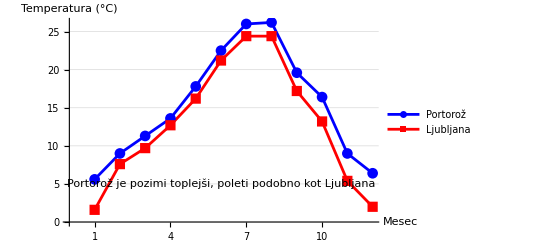

```mathematica
(*---Graf povprečnih temperatur za obe mesti skupaj---*)ListLinePlot[{portorozData["Povprečna temperatura"],ljubljanaData["Povprečna temperatura"]},PlotStyle->{Blue,Red},PlotMarkers->Automatic,AxesLabel->{"Mesec","Temperatura (°C)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],Epilog->{Text["Portorož je pozimi toplejši, poleti podobno kot Ljubljana",{6,5},Background->White]}]
```

```mathematica
(*Portorož pozimi ostaja blago (~5–9 °C),poleti pa doseže~26 °C.Ljubljana pozimi pogosto pod 0 °C,poleti pa približno enako topla kot Portorož.Razlika med mestoma je večja pozimi kot poleti.*)
```

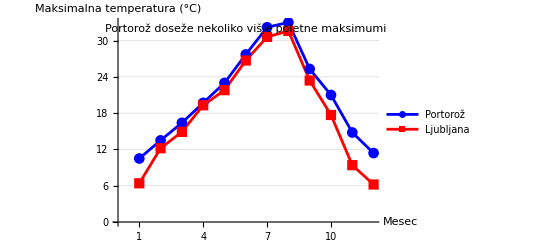

```mathematica
(*Graf povprečne maksimalne temperature za obe mesti*)ListLinePlot[{portorozData["Povprečna maksimalna temperatura"],ljubljanaData["Povprečna maksimalna temperatura"]},PlotStyle->{Blue,Red},PlotMarkers->Automatic,AxesLabel->{"Mesec","Maksimalna temperatura (°C)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],Epilog->{Text["Portorož doseže nekoliko višje poletne maksimumi",{6,32},Background->White]}]
```

```mathematica
(*Poleti je Portorož nekoliko toplejši od Ljubljane (~32–33 °C).Pozimi je Ljubljana hladnejša kot Portorož (~6–15 °C).*)
```

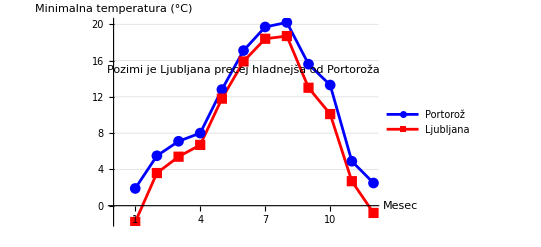

```mathematica
(*Graf povprečne minimalne temperature za obe mesti*)ListLinePlot[{portorozData["Povprečna minimalna temperatura"],ljubljanaData["Povprečna minimalna temperatura"]},PlotStyle->{Blue,Red},PlotMarkers->Automatic,AxesLabel->{"Mesec","Minimalna temperatura (°C)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],Epilog->{Text["Pozimi je Ljubljana precej hladnejša od Portoroža",{6,15},Background->White]}]
```

```mathematica
(*Najnižje temperature pozimi pogosto pod 0 °C v Ljubljani,medtem ko je Portorož blago (~2 °C).Poleti so noči v Portorožu nekoliko toplejše kot v Ljubljani (~20 °C vs. ~18 °C).*)
```

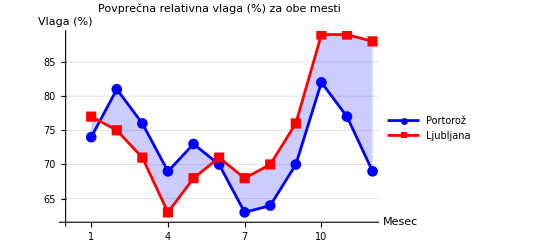

```mathematica
(*povprečne relativne vlage za obe mesti skupaj*)ListLinePlot[{portorozData["Povprečna relativna vlaga"],(*Portorož*)ljubljanaData["Povprečna relativna vlaga"]  (*Ljubljana*)},PlotStyle->{Blue,Red},PlotMarkers->Automatic,Filling->{1->{2}},(*senčeno območje med modro in rdečo linijo*)AxesLabel->{"Mesec","Vlaga (%)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],PlotLabel->"Povprečna relativna vlaga (%) za obe mesti"]
```

```mathematica
(*Senčeno območje prikazuje razliko med mesti:Portorož je bolj vlažen pozimi,Ljubljana ima večje nihanje skozi leto.Najvišja vlažnost je v jesenskih in zimskih mesecih,najnižja poleti.*)
```

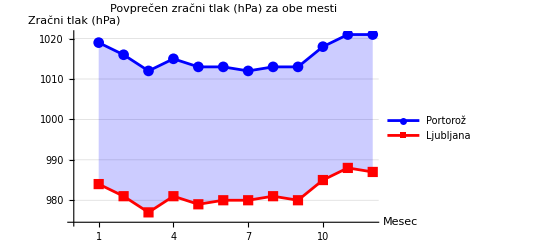

```mathematica
(*povprečnega zračnega tlaka za obe mesti skupaj*)ListLinePlot[{portorozData["Povprečen zračni tlak"],(*Portorož*)ljubljanaData["Povprečen zračni tlak"]   (*Ljubljana*)},PlotStyle->{Blue,Red},PlotMarkers->Automatic,Filling->{1->{2}},(*senčeno območje med modro in rdečo linijo*)AxesLabel->{"Mesec","Zračni tlak (hPa)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],PlotLabel->"Povprečen zračni tlak (hPa) za obe mesti"]
```

```mathematica
(*Portorož ima nekoliko višji zračni tlak skozi vse leto (~1012–1021 hPa).Ljubljana ima nižji zračni tlak (~977–988 hPa),kar je značilno za celinske regije.Senčeno območje prikazuje razliko med mestoma skozi vse leto.*)
```

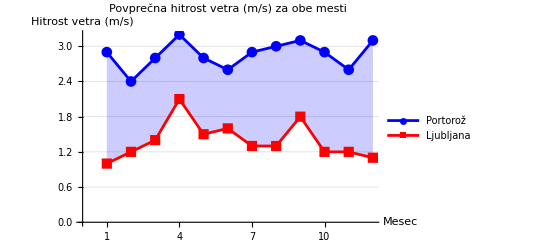

```mathematica
(* povprečne hitrosti vetra za obe mesti skupaj*)ListLinePlot[{portorozData["Povprečna hitrost vetra"],(*Portorož*)ljubljanaData["Povprečna hitrost vetra"]  (*Ljubljana*)},PlotStyle->{Blue,Red},PlotMarkers->Automatic,Filling->{1->{2}},(*senčeno območje med modro in rdečo linijo*)AxesLabel->{"Mesec","Hitrost vetra (m/s)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],PlotLabel->"Povprečna hitrost vetra (m/s) za obe mesti"]
```

```mathematica
(*Portorož ima rahlo višje povprečne hitrosti vetra (2.4–3.1 m/s),kar je pričakovano za obalno območje.Ljubljana ima nižje hitrosti vetra (1–1.8 m/s),značilno za zaledje.Senčeno območje jasno pokaže razliko med mesti.*)
```

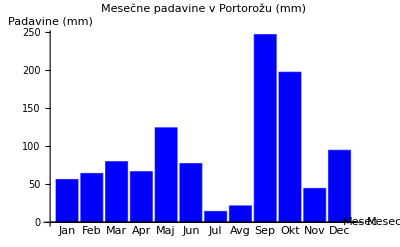

```mathematica
(*Stolpčni graf količine padavin za Portorož*)BarChart[portorozData["Količina padavin"],ChartLabels->Placed[meseci,Below],ChartStyle->Blue,PlotLabel->"Mesečne padavine v Portorožu (mm)",AxesLabel->{"Mesec","Padavine (mm)"}]
```

```mathematica
(*Največ padavin je septembra (~246 mm) in oktobra (~197 mm).Julij in avgust so suhi (~14–22 mm).*)
```

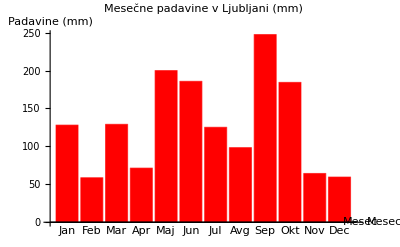

```mathematica
(*Stolpčni graf količine padavin za Ljubljano*)BarChart[ljubljanaData["Količina padavin"],ChartLabels->Placed[meseci,Below],ChartStyle->Red,PlotLabel->"Mesečne padavine v Ljubljani (mm)",AxesLabel->{"Mesec","Padavine (mm)"}]
```

```mathematica
(*Največ padavin je septembra (~248 mm) in maja (~200 mm).Februar in december sta razmeroma suha (~59 mm).*)
```

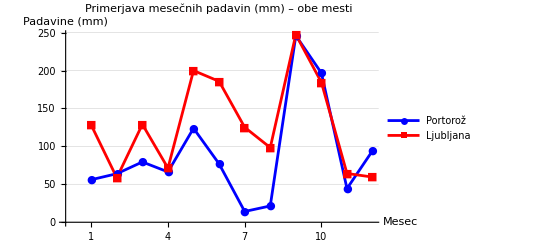

```mathematica
(*Line plot padavin za obe mesti skupaj*)ListLinePlot[{portorozData["Količina padavin"],(*Portorož*)ljubljanaData["Količina padavin"]   (*Ljubljana*)},PlotStyle->{Blue,Red},PlotMarkers->{"●","■"},(*točke na liniji*)AxesLabel->{"Mesec","Padavine (mm)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],PlotLabel->"Primerjava mesečnih padavin (mm) – obe mesti"]
```

```mathematica
(*Portorož ima največ padavin septembra in oktobra,najmanj julija/avgusta.Ljubljana ima največ padavin maja in septembra,najmanj februarja in decembra.Točke na linijah omogočajo hitro vizualno primerjavo mesečnih razlik.*)
```

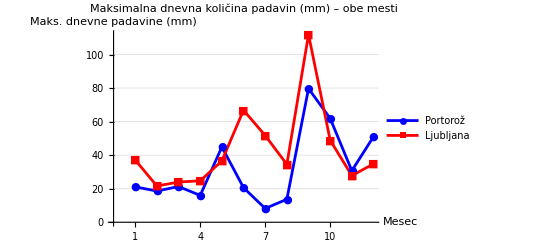

```mathematica
(*Line plot maksimalne dnevne količine padavin za obe mesti skupaj*)ListLinePlot[{portorozData["Maksimalna dnevna količina padavin"],(*Portorož*)ljubljanaData["Maksimalna dnevna količina padavin"]   (*Ljubljana*)},PlotStyle->{Blue,Red},PlotMarkers->{"●","■"},AxesLabel->{"Mesec","Maks. dnevne padavine (mm)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],PlotLabel->"Maksimalna dnevna količina padavin (mm) – obe mesti"]
```

```mathematica
(*Ljubljana doseže ekstremne vrednosti maja in septembra (~112 mm),Portorož pa septembra (~80 mm).Graf jasno pokaže,kateri mesec ima največje posamezne padavine v obeh mestih.Točke omogočajo hitro primerjavo mesečnih maksimumov.*)
```

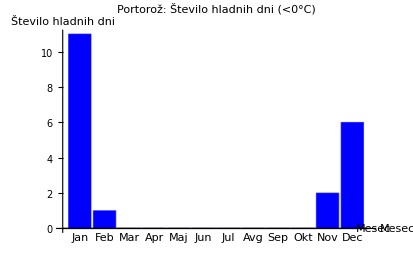
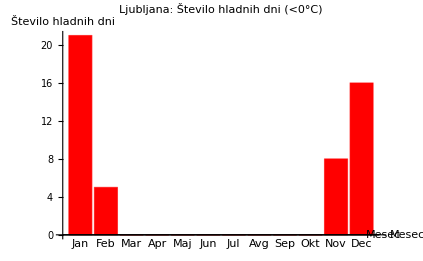

```mathematica
(*Stolpčni graf števila hladnih dni za Portorož*)grafPortoroz=BarChart[portorozData["Število hladnih dni"],ChartLabels->Placed[meseci,Below],ChartStyle->Blue,PlotLabel->"Portorož: Število hladnih dni (<0°C)",AxesLabel->{"Mesec","Število hladnih dni"},ImageSize->500];

(*Stolpčni graf števila hladnih dni za Ljubljano*)
grafLjubljana=BarChart[ljubljanaData["Število hladnih dni"],ChartLabels->Placed[meseci,Below],ChartStyle->Red,PlotLabel->"Ljubljana: Število hladnih dni (<0°C)",AxesLabel->{"Mesec","Število hladnih dni"},ImageSize->500];

(*Prikaz obeh grafov skupaj v vrstici*)
Row[{grafPortoroz,grafLjubljana}]
```

```mathematica
(*Ljubljana ima bistveno več hladnih dni pozimi (januar,december),tudi februar nekoliko.Portorož ima le nekaj hladnih dni v januarju in decembru.*)
```

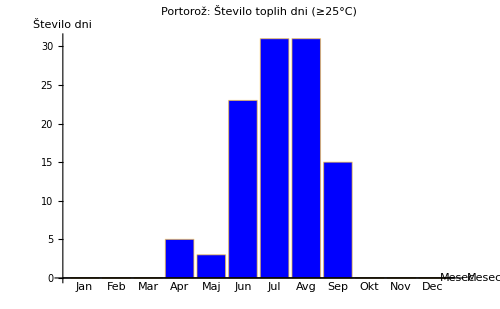
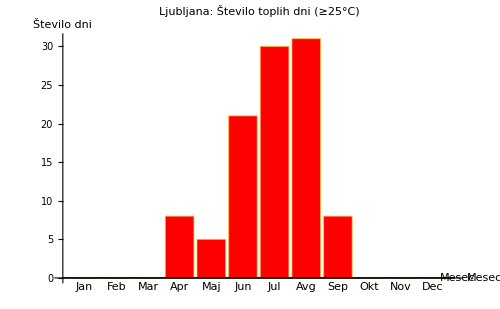

```mathematica
(*---Število toplih dni (maks.temp≥25°C)---*)grafTopliDniPortoroz=BarChart[portorozData["Število toplih dni"],ChartLabels->Placed[meseci,Below],ChartStyle->Blue,PlotLabel->"Portorož: Število toplih dni (≥25°C)",AxesLabel->{"Mesec","Število dni"},ImageSize->500];

grafTopliDniLjubljana=BarChart[ljubljanaData["Število toplih dni"],ChartLabels->Placed[meseci,Below],ChartStyle->Red,PlotLabel->"Ljubljana: Število toplih dni (≥25°C)",AxesLabel->{"Mesec","Število dni"},ImageSize->500];

Row[{grafTopliDniPortoroz,grafTopliDniLjubljana}]
```

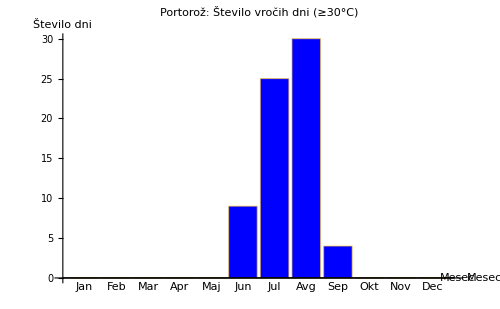
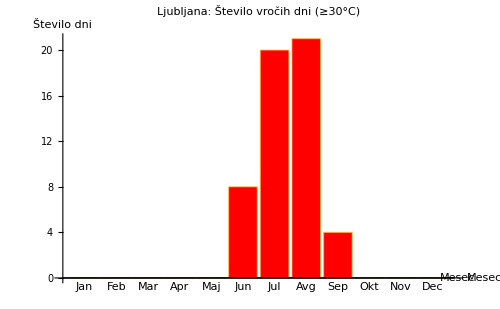

```mathematica
(*---Število vročih dni (maks.temp≥30°C)---*)grafVrociDniPortoroz=BarChart[portorozData["Število vročih dni"],ChartLabels->Placed[meseci,Below],ChartStyle->Blue,PlotLabel->"Portorož: Število vročih dni (≥30°C)",AxesLabel->{"Mesec","Število dni"},ImageSize->500];

grafVrociDniLjubljana=BarChart[ljubljanaData["Število vročih dni"],ChartLabels->Placed[meseci,Below],ChartStyle->Red,PlotLabel->"Ljubljana: Število vročih dni (≥30°C)",AxesLabel->{"Mesec","Število dni"},ImageSize->500];

Row[{grafVrociDniPortoroz,grafVrociDniLjubljana}]
```

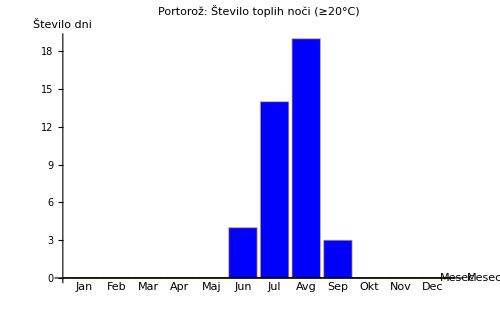
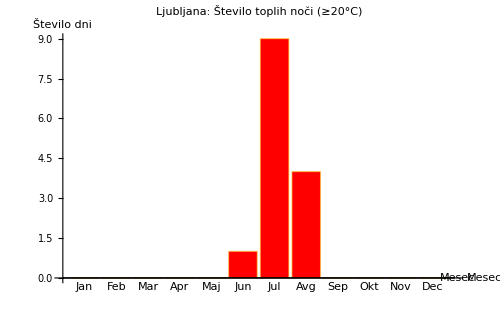

```mathematica
(*---Število toplih noči (min.temp≥20°C)---*)grafTopleNociPortoroz=BarChart[portorozData["Število toplih noči"],ChartLabels->Placed[meseci,Below],ChartStyle->Blue,PlotLabel->"Portorož: Število toplih noči (≥20°C)",AxesLabel->{"Mesec","Število dni"},ImageSize->500];

grafTopleNociLjubljana=BarChart[ljubljanaData["Število toplih noči"],ChartLabels->Placed[meseci,Below],ChartStyle->Red,PlotLabel->"Ljubljana: Število toplih noči (≥20°C)",AxesLabel->{"Mesec","Število dni"},ImageSize->500];

Row[{grafTopleNociPortoroz,grafTopleNociLjubljana}]
```

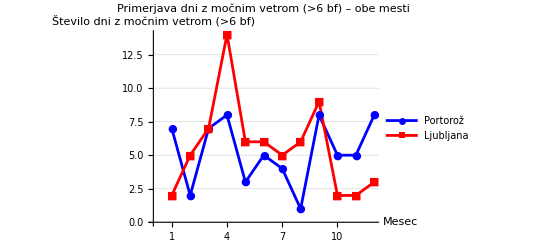

```mathematica
(*dni z močnim vetrom za obe mesti skupaj*)ListLinePlot[{portorozData["Število dni z močnim vetrom"],(*Portorož*)ljubljanaData["Število dni z močnim vetrom"]   (*Ljubljana*)},PlotStyle->{Blue,Red},PlotMarkers->{"●","■"},AxesLabel->{"Mesec","Število dni z močnim vetrom (>6 bf)"},Ticks->{Range[12],Automatic},GridLines->Automatic,PlotLegends->Placed[{"Portorož","Ljubljana"},Above],PlotLabel->"Primerjava dni z močnim vetrom (>6 bf) – obe mesti"]
```

```mathematica
(*Portorož ima več dni z močnim vetrom pozimi in v jeseni.Ljubljana ima nekaj več dni spomladi in jeseni,a povprečno manj kot obala*)
```

```mathematica
(*Število dni s padavinami nad 0.1 mm*)
```

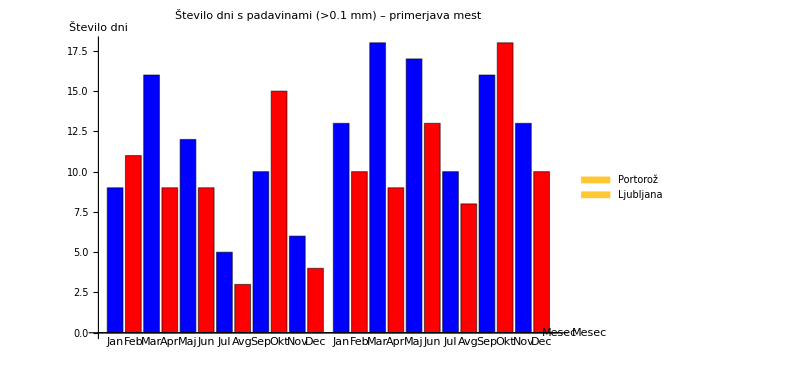

```mathematica
dniPadavin=Table[{portorozData["Število dni s padavinami nad 0.1 mm"][[i]],ljubljanaData["Število dni s padavinami nad 0.1 mm"][[i]]},{i,12}];


BarChart[{Legended[Table[dniPadavin[[i,1]],{i,12}],"Portorož"],Legended[Table[dniPadavin[[i,2]],{i,12}],"Ljubljana"]},ChartLayout->"Grouped",ChartLabels->Placed[meseci,Below],ChartStyle->{Blue,Red},PlotLabel->"Število dni s padavinami (>0.1 mm) – primerjava mest",AxesLabel->{"Mesec","Število dni"},ImageSize->600]
```

```mathematica
(*Število dni s padavinami>10 mm*)
```

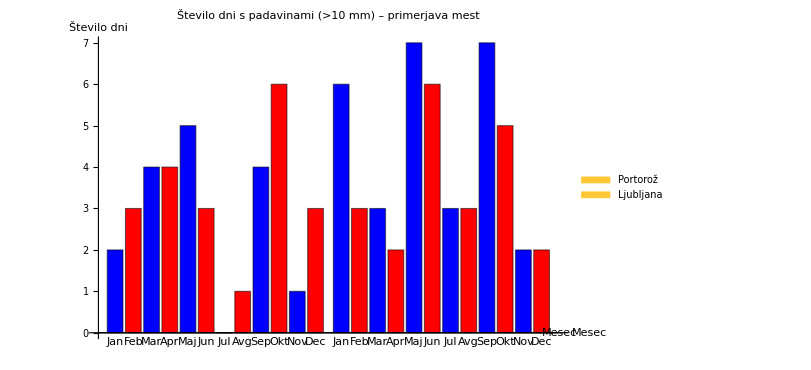

```mathematica
dniPadavin10=Table[{portorozData["Število dni s padavinami nad 10 mm"][[i]],ljubljanaData["Število dni s padavinami nad 10 mm"][[i]]},{i,12}];

BarChart[{Legended[Table[dniPadavin10[[i,1]],{i,12}],"Portorož"],Legended[Table[dniPadavin10[[i,2]],{i,12}],"Ljubljana"]},ChartLayout->"Grouped",ChartLabels->Placed[meseci,Below],ChartStyle->{Blue,Red},PlotLabel->"Število dni s padavinami (>10 mm) – primerjava mest",AxesLabel->{"Mesec","Število dni"},ImageSize->600]
```

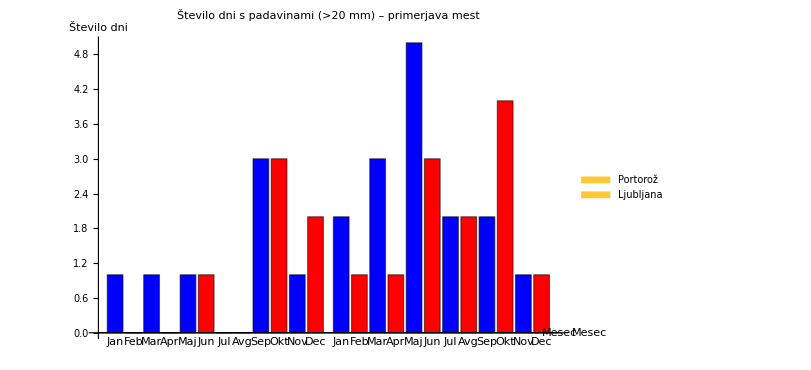

```mathematica
(*Število dni s padavinami>20 mm*)
dniPadavin20=Table[{portorozData["Število dni s padavinami nad 20 mm"][[i]],ljubljanaData["Število dni s padavinami nad 20 mm"][[i]]},{i,12}];

BarChart[{Legended[Table[dniPadavin20[[i,1]],{i,12}],"Portorož"],Legended[Table[dniPadavin20[[i,2]],{i,12}],"Ljubljana"]},ChartLayout->"Grouped",ChartLabels->Placed[meseci,Below],ChartStyle->{Blue,Red},PlotLabel->"Število dni s padavinami (>20 mm) – primerjava mest",AxesLabel->{"Mesec","Število dni"},ImageSize->600]
```

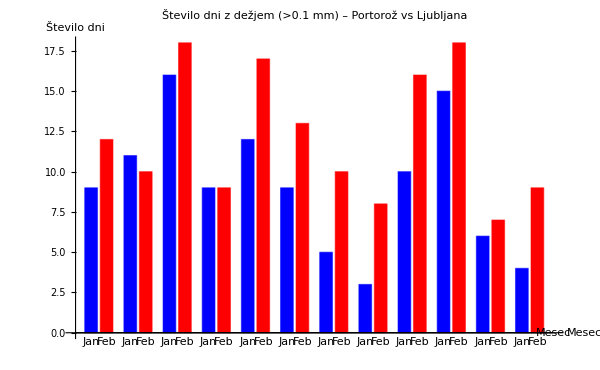

```mathematica
(*število dni z dežjem nad 0.1 mm*)
(*Priprava podatkov:vsak mesec dve vrednosti*)dniDezja=Table[{portorozData["Število dni z dežjem nad 0.1 mm"][[i]],ljubljanaData["Število dni z dežjem nad 0.1 mm"][[i]]},{i,12}];

(*Grupiran stolpčni graf za primerjavo*)
BarChart[dniDezja,ChartLayout->"Grouped",(*stolpci eden zraven drugega*)ChartLabels->Placed[meseci,Below],ChartStyle->{Blue,Red},PlotLabel->"Število dni z dežjem (>0.1 mm) – Portorož vs Ljubljana",AxesLabel->{"Mesec","Število dni"},ImageSize->600]
```

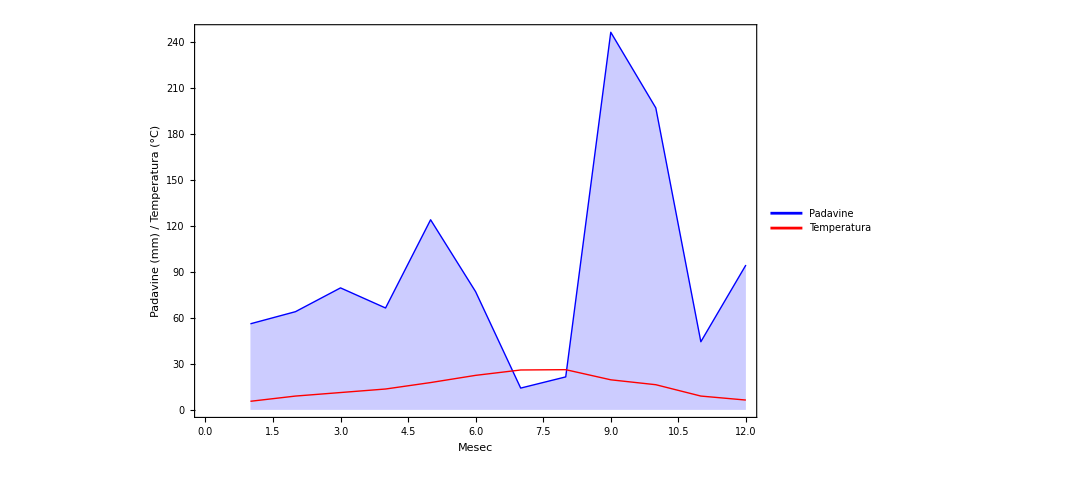

```mathematica
(*primerjava padavin in temperatur za Portorož*)
padavine=portorozData["količina padavin (mm)"];
temperatura=portorozData["povprečna temperatura zraka na 2 m (°C)"];
meseci=Range[12];

ListLinePlot[{Transpose[{meseci,padavine}],(*Padavine*)Transpose[{meseci,temperatura}]     (*Temperatura*)},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},Filling->{1->Axis},(*modra črta do x osi*)Frame->True,FrameLabel->{"Mesec","Padavine (mm) / Temperatura (°C)"},FrameTicks->{Automatic,Automatic,Thread[meseci->meseci],(*X-osa:1,2,...,12*)Automatic},PlotMarkers->None,PlotLegends->{"Padavine","Temperatura"},ImageSize->{800,400}]
```

```mathematica
(*Graf jasno prikazuje sezonske semembe:poletni meseci (Julij,Avgust) so najtoplejši,rati pa imajo najmanj padavin.*)
(*Jesenski in spomladanski meseci (Maj,September,Oktober) imajo več padavin,temperatura pa je zmerna.*)
```

```mathematica
(*Jesenski in spomladanski meseci (Maj,September,Oktober) imajo več padavin,temperatura pa je zmerna.*)
```

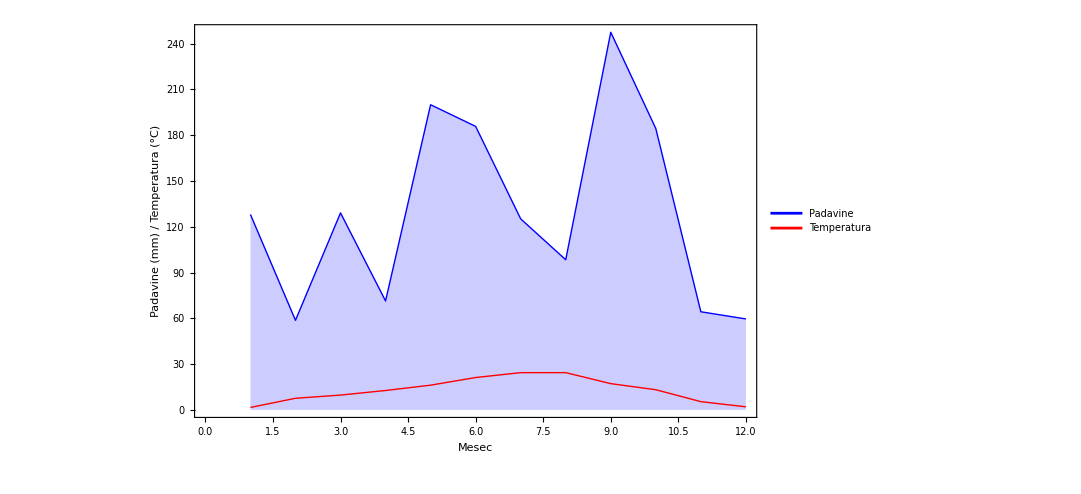

```mathematica
(*seznam vseh podatkov za Ljubljano*)padavineLj={128.1,58.7,129.1,71.4,200,185.8,125.2,98.4,247.5,184.4,64.3,59.6};
temperaturaLj={1.6,7.6,9.7,12.7,16.2,21.2,24.4,24.4,17.2,13.2,5.4,2};
meseci=Range[12];

(*primerjava padavin in temperatur za Ljubljano*)
ListLinePlot[{Transpose[{meseci,padavineLj}],(*Padavine*)Transpose[{meseci,temperaturaLj}]     (*Temperatura*)},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},Filling->{1->Axis},(*modra črta do x osi*)Frame->True,FrameLabel->{"Mesec","Padavine (mm) / Temperatura (°C)"},FrameTicks->{Automatic,Automatic,Thread[meseci->meseci],(*X-osa:1–12*)Automatic},PlotMarkers->None,PlotLegends->{"Padavine","Temperatura"},ImageSize->{800,400}]
```

```mathematica
(*Največ padavin je zaznati spomladi (Maj) in jeseni (September,Oktober),medtem ko so najtoplejši meseci Julij in Avgust–temperatura je visoka,padavin je pa manj kot spomladi,vendar več kot v Portorožu.*)
(*V Ljubljani je poleti še vedno nekoliko mokro,čeprav so temperature visoke,kar je drugače kot v Portorožu,kjer so poleti padavine minimalne.*)
```